## Set 5, Part 2: Symbolic Algebra with Mathematica

## sin(x) and cos(x) in series form

We want to compare the series expansions of sin(x) and cos(x) to the actual functions. We define series versions of sin(x) and cos(x) about x = 0.

```mathematica
SerSin[x_,n_]:=Normal[Series[Sin[y],{y,0,n}]]/.y->x
```

```mathematica
SerCos[x_,n_]:=Normal[Series[Cos[y],{y,0,n}]]/.y->x
```

We compare the series and normal versions of sin(x), plotting the error as a function of x for various n.

```mathematica
SinError[x_,n_]:=Abs[N[SerSin[x,n]-Sin[x]]]
```

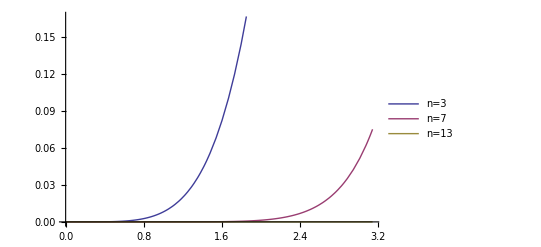

```mathematica
Plot[{SinError[x,3],SinError[x,7],SinError[x,13]},{x,0,π},PlotLegends->{"n=3","n=7","n=13"}]
```

As we go substantially far away from the point of expansion (x = 0), the higher-order approximations are substantially less accurate.

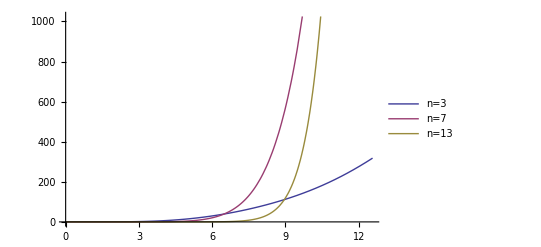

```mathematica
Plot[{SinError[x,3],SinError[x,7],SinError[x,13]},{x,0,4π},PlotLegends->{"n=3","n=7","n=13"}]
```

Squaring

We check whether sin^2(x)+cos^2(x)=1 holds for the series versions.

```mathematica
Squared1[x_,n_]:=(SerSin[x,n])^2+(SerCos[x,n])^2
```

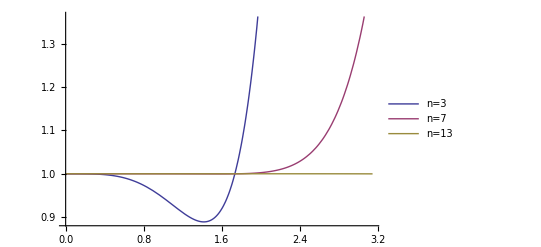

```mathematica
Plot[{Squared1[x,3],Squared1[x,7],Squared1[x,13]},{x,0,π},PlotLegends->{"n=3","n=7","n=13"}]
```

As expected, when x is close to 0 (the point of series expansion), a higher n yields a more accurate result.

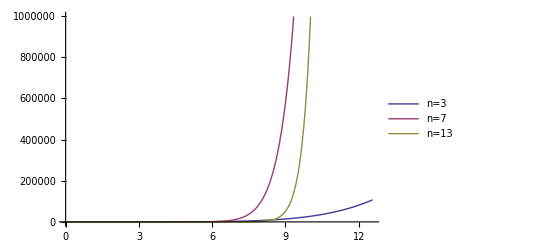

```mathematica
Plot[{Squared1[x,3],Squared1[x,7],Squared1[x,13]},{x,0,4π},PlotLegends->{"n=3","n=7","n=13"}]
```

As before, moving far away from the point of expansion causes the higher-order approximations to become far less accurate, yielding values on the order of 10^5 and 10^6 instead of 1. We make another attempt using the series expansion for the trigonometric functions already squared:

```mathematica
SerSinSq[x_,n_]:=Normal[Series[(Sin[y])^2,{y,0,n}]]/.y->x
```

```mathematica
SerCosSq[x_,n_]:=Normal[Series[(Cos[y])^2,{y,0,n}]]/.y->x
```

```mathematica
Squared2[x_,n_]:=SerSinSq[x,n]+SerCosSq[x,n]
```

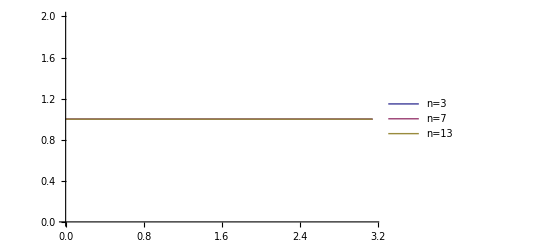

```mathematica
Plot[{Squared2[x,3],Squared2[x,7],Squared2[x,13]},{x,0,π},PlotLegends->{"n=3","n=7","n=13"},PlotRange->{0,2}]
```

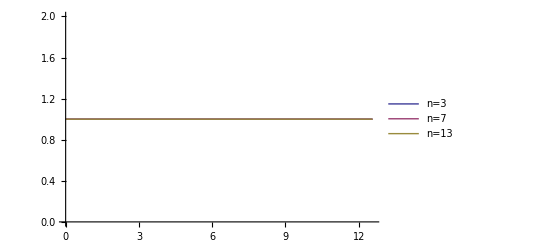

```mathematica
Plot[{Squared2[x,3],Squared2[x,7],Squared2[x,13]},{x,0,4π},PlotLegends->{"n=3","n=7","n=13"},PlotRange->{0,2}]
```

It seems that using the series expansion of the trigonometric function already squared yields the expected result of 1, while squaring the series expansion creates deviations. This is expected since the series expansion of sin^2(x) is not the square of the series expansion of sin(x), as squaring the expansion of sin(x) would introduces higher-order terms that create large errors when x is far from 0.

Euler Angles

We define 3-dimensional rotation matrices about the x, y, and z axes:

```mathematica
Rx[θ_]:=({{1, 0, 0}, {0, Cos[θ], Sin[θ]}, {0, -Sin[θ], Cos[θ]}})
```

```mathematica
Ry[ζ_]:=({{Cos[ζ], 0, Sin[ζ]}, {0, 1, 0}, {-Sin[ζ], 0, Cos[ζ]}})
```

```mathematica
Rz[ϕ_]:=({{Cos[ϕ], Sin[ϕ], 0}, {-Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}})
```

A three-dimensional rotation can be expressed as a rotation around the z axis, followed by a rotation around the x axis, followed by a rotation around the z axis:

```mathematica
Rot3[ψ_,θ_,ϕ_]:=Rz[ψ].Rx[θ].Rz[ϕ]
```

```mathematica
Simplify[Rot3[ψ,θ,ϕ]]
```

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | sin(θ) sin(ψ)
-cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | cos(ψ) sin(θ)
sin(θ) sin(ϕ) | -cos(ϕ) sin(θ) | cos(θ))

An inverse rotation would simply be undoing these rotations (in reverse order):

```mathematica
Rot3Inverse[ψ_,θ_,ϕ_]:=Rz[-ϕ].Rx[-θ].Rz[-ψ]
```

```mathematica
Simplify[Rot3Inverse[ψ,θ,ϕ]]
```

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | -cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | sin(θ) sin(ϕ)
cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ϕ) sin(θ)
sin(θ) sin(ψ) | cos(ψ) sin(θ) | cos(θ))

As expected, this is equal to the inverse of the original 3D rotation matrix:

```mathematica
Simplify[Inverse[Rot3[ψ,θ,ϕ]]]
```

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | -cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | sin(θ) sin(ϕ)
cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ϕ) sin(θ)
sin(θ) sin(ψ) | cos(ψ) sin(θ) | cos(θ))

```mathematica
Simplify[Inverse[Rot3[ψ,θ,ϕ]] - Rot3Inverse[ψ,θ,ϕ]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)